3/16/22 OK again no electric field version for SR plot AMJ

```mathematica
ClearAll["Global`*"]
Current = 100.0;
Mu0 = 4 π 10^-7;
Epsilon = 8.85 10^-12;
q = 2.0 10^-12;              (* coulombs   *)
RhoL = 0.0 10^-14;
Mass = 5.0×10^-19 ;     (* kilograms  *)
a = 5.0 10^-4 ;
dWire = 20. a;
rWire = a;
```

```mathematica
Vx0 = 0.;
Vx = Vx0;   (* meters/second *)
Vz0 = 50.;
Vz = Vz0;
x = 40a;(* meters from the wire *)
z = 0;  
Print[ "pq Difference Max = ",  5 10^-7 * q * Current]
Print[ "2 times Pq Initital = ",  2 * Mass * Vz0]
Print[ "KE Initial = ",  0.5 * Mass * Vz0 * Vz0]
Print[ "Delta KE after  Volts = ",  q * 0.4 * RhoL / (1.0 10^-11)  ]
```

pq Difference Max = 1.×10^-16

2 times Pq Initital = 5.×10^-17

KE Initial = 6.25×10^-16

Delta KE after  Volts = 0.

```mathematica
numElements = 101;
VxList = Table[0.0, {i, numElements}];
VzList = Table[0.0, {i, numElements}];
XList = Table[0.0, {i, numElements}];
ZList = Table[0.0, {i, numElements}];
TimeList = Table[0.0, {i, numElements}];
VDiffList = Table[0.0, {i, numElements}];
oneList = Table[{{i, i}, {2 i, -2 i}}, {i, 1, numElements}];
```

```mathematica
deltaT = 2.0 10^-9;
TimeNow = 0.;
```

```mathematica
n = 0;
m =1;
xOld = 5.;
xNew = 0.;
Test = 0.;
testElement = 5000;    (*  How many timesteps between recorded elements  *)
numTimeSteps = testElement * (numElements -1) + 1   (* the +1 is because we are starting with n=0 
                                                 also (numElements - 1) since starting with n = 0 *)
Do[
ByTotal[x_] = (Mu0 Current)/(2 π (x-dWire/2.))   +  (- Mu0 Current)/(2 π (x +dWire/2.)); (*  By due to wires at x = +/- dWire/2  *)
ExTotal[x_] = RhoL/(2 π Epsilon(x-dWire/2.))   +  (- RhoL)/(2 π Epsilon(x +dWire/2.));  

Fz[x_] = q Vx ByTotal[x] ;   (* with By in the x-z plane there will only be x and z magnetic forces *)
Fx[x_] = -q Vz ByTotal[x] + q ExTotal[x];  (* Vz crossed with By gives the negative sign *)
(* Fx[x_] = -q Vz ByTotal[x];  *)


TimeNow = TimeNow + deltaT;
xAcceleration = Fx[x]/Mass;
Vx = Vx + (xAcceleration deltaT);
xOld = x;
x = x + Vx deltaT;
xNew = x;
If[xNew > xOld && Test < 1., 
{ timeMin = TimeNow;
xMin = xOld;
VzMin = Vz;
Test = 2.; }, {}]

   zAcceleration = Fz[x]/Mass;
Vz = Vz + (zAcceleration deltaT);
z = z + Vz deltaT; 
test = Mod[n,testElement];
Vtotal = Sqrt[Vx^2 + Vz^2];
If[ test == 0,{  (*  Print[n, " ",Vx, "  ", x, "  ", Vz, "  ", z, "  ", TimeNow, "  ",Vtotal-Vz0]; *)
If [Mod[n, 50000] ==0, Print[n], {}];  (* This is so I can watch the program run  *)
TimeList[[m]] = TimeNow; 
VxList[[m]] = Vx;
VzList[[m]] = Vz;
XList[[m]] = x;
ZList[[m]] = z;
oneList[[m]][[1]][[1]] =  z;
oneList[[m]][[1]][[2]] =  x;
oneList[[m]][[2]][[1]] =  Vz;
oneList[[m]][[2]][[2]] =  Vx;
VDiffList[[m]] = (Vtotal-Vz0)/ Vz0 * 100.;m++}
        , {}  ] ;
n++
  ,   numTimeSteps  ]
```

500001

0

50000

100000

150000

200000

250000

300000

350000

400000

450000

500000

```mathematica
VxTimeData = Transpose[{TimeList,VxList}];
VzTimeData = Transpose[{TimeList,VzList}];
pZTimeData = Transpose[{TimeList,Mass * VzList}];
```

```mathematica
xTimeData = Transpose[{TimeList,XList}];
zTimeData = Transpose[{TimeList,ZList}];
vDiffTimeData = Transpose[{TimeList,VDiffList}];
```

```mathematica
Print[ "xMinimum = ",  xMin]
Print[ "VzMinimum = ",  VzMin]
```

xMinimum = 0.00707584

VzMinimum = -50.0022

```mathematica
VzTimeData;
```

```mathematica
xTimeData;
```

```mathematica
xzData = Transpose[{ZList,XList}];
```

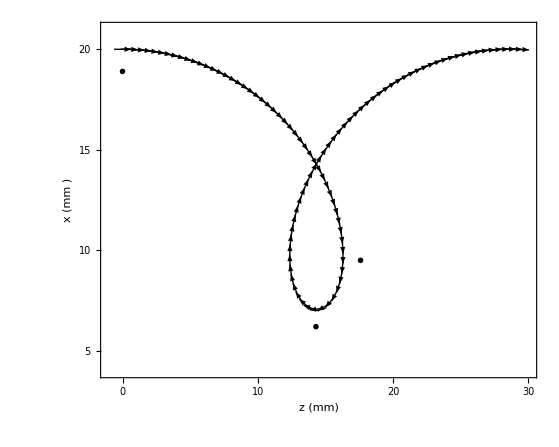

```mathematica
circle[text_,pos_]:=Inset[Graphics[{Text[text],Circle[]},ImageSize->25],pos]
SRTraj = ListVectorPlot[oneList,VectorPoints->All, VectorSizes->Tiny,VectorColorFunction->None,  VectorStyle->Black,FrameTicks->{   {{#,1000 #}&/@FindDivisions[{.004,.021},5],None}  ,{{#,1000 #}&/@FindDivisions[{0.,.030},5],Automatic}}, FrameLabel-> {"z (mm)","x (mm )"}, LabelStyle->Directive[Black, FontSize -> 16]  , AspectRatio-> 0.8,Epilog-> {circle[Style[1, Bold, 14], {0.00, 0.0189}  ],circle[Style[2, Bold, 14], {0.0176, 0.0095}  ] ,circle[Style[3, Bold, 14], {0.0143, 0.0062}  ]}, PlotRange->{ {-0.001, 0.03}, {.004, 0.021} } ]
```

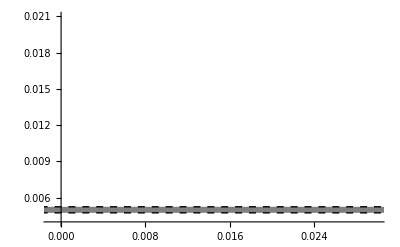

```mathematica
PlotWire = Plot[ { dWire/2.-rWire/2.0, dWire/2.+rWire/2.0 } ,   {z,-0.02, 0.06}, Filling ->{1->{{2}, Gray}},  PlotRange->{ {-0.001, 0.03}, {.004, 0.021} },PlotStyle->{{Black, Thick, Dashed}, {Black, Thick,Dashed}} ]
```

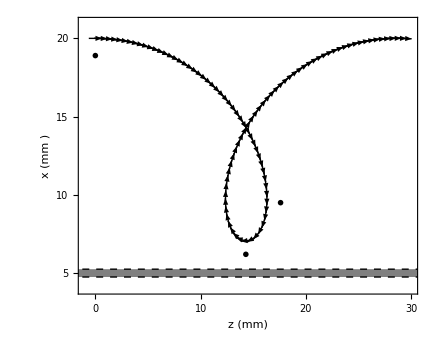

```mathematica
Show[SRTraj, PlotWire]
```

```mathematica
(* since the contributions to Az(x) from the two wires cancel for x = 0, Az(0) = 0, and we integrate
the B field from x = 0 to whatever x we want, to get Az(x)  
Reminder: dWire is the distance between the wires, rWire is the wire radius where I = 0 is assumed *) 

hFieldY1[x_]:=If[Norm[x-dWire/2] > rWire, Sign[x-dWire/2.] (Current/(2 Pi Abs[x-dWire/2.]  )), 0.] ;
hFieldY2[x_]:= (-Current)/(2 Pi (x+dWire/2.)  ) ;    (* Sign[] not needed since always have x > 0  *)
hFieldYTotal[x_] := hFieldY1[x] +hFieldY2[x];
AofX[x_] := -Integrate[Mu0 hFieldYTotal[xTemp], {xTemp, 0, x}]

AofXTable = Table[0.0, {i, numElements}];
Do[ {
x= xTimeData[[n]][[2]];
AofXTable[[n]] = AofX[x];
tPrint = Mod[n, 10];
If[ tPrint== 0, Print[n, "   ",x, "   ", AofXTable[[n]]  ], {} ]; 
},
{n,1, numElements}]
```

10   0.019566   0.0000104535

20   0.0180339   0.0000113883

30   0.0152868   0.0000135822

40   0.0111594   0.0000192904

50   0.00708033   0.0000351811

60   0.0109304   0.0000197628

70   0.015124   0.0000137401

80   0.0179336   0.0000114555

90   0.019521   0.0000104787

100   0.0200018   0.0000102156

```mathematica
q AofXTable
```

{2.0433×10^-17,2.04387×10^-17,2.04558×10^-17,2.04844×10^-17,2.05246×10^-17,2.05765×10^-17,2.06404×10^-17,2.07165×10^-17,2.08053×10^-17,2.0907×10^-17,2.10221×10^-17,2.11511×10^-17,2.12947×10^-17,2.14535×10^-17,2.16282×10^-17,2.18198×10^-17,2.20293×10^-17,2.22577×10^-17,2.25063×10^-17,2.27766×10^-17,2.30701×10^-17,2.33887×10^-17,2.37345×10^-17,2.41098×10^-17,2.45173×10^-17,2.49601×10^-17,2.54418×10^-17,2.59665×10^-17,2.65388×10^-17,2.71644×10^-17,2.78496×10^-17,2.86021×10^-17,2.94307×10^-17,3.0346×10^-17,3.13608×10^-17,3.249×10^-17,3.37521×10^-17,3.51692×10^-17,3.67679×10^-17,3.85808×10^-17,4.0647×10^-17,4.30125×10^-17,4.57297×10^-17,4.88522×10^-17,5.24216×10^-17,5.6434×10^-17,6.07686×10^-17,6.50642×10^-17,6.85923×10^-17,7.03621×10^-17,6.97089×10^-17,6.68923×10^-17,6.28461×10^-17,5.84643×10^-17,5.42726×10^-17,5.04875×10^-17,4.71564×10^-17,4.42533×10^-17,4.17277×10^-17,3.95256×10^-17,3.75978×10^-17,3.59019×10^-17,3.44023×10^-17,3.30697×10^-17,3.18798×10^-17,3.08128×10^-17,2.9852×10^-17,2.89836×10^-17,2.81962×10^-17,2.74801×10^-17,2.68271×10^-17,2.62302×10^-17,2.56835×10^-17,2.51819×10^-17,2.47211×10^-17,2.42972×10^-17,2.39069×10^-17,2.35474×10^-17,2.32161×10^-17,2.29109×10^-17,2.26298×10^-17,2.2371×10^-17,2.21331×10^-17,2.19148×10^-17,2.17148×10^-17,2.15321×10^-17,2.13658×10^-17,2.1215×10^-17,2.10791×10^-17,2.09574×10^-17,2.08493×10^-17,2.07544×10^-17,2.06723×10^-17,2.06025×10^-17,2.05448×10^-17,2.0499×10^-17,2.04648×10^-17,2.04422×10^-17,2.0431×10^-17,2.04311×10^-17,2.04427×10^-17}

```mathematica
qAofXTimeData = Transpose[{TimeList,q * AofXTable}];
```

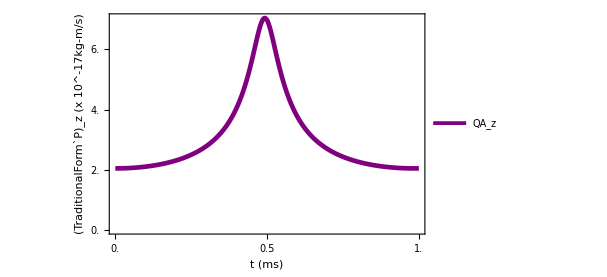

```mathematica
legendsa={StringForm["````","Q",Subscript["A","z"]]};P10a = ListLinePlot[{qAofXTimeData},  FrameLabel -> {"t (ms)", "(TraditionalForm`P)_z   (x 10^-17kg-m/s)"}, Frame -> True, FrameTicks->  {    {{#,10^17 #}&/@FindDivisions[{-2. 10^-17,7. 10^-17},9] //N,Automatic},{{#,1000 #}&/@FindDivisions[{0.,.002},5] //N,Automatic}   } , LabelStyle->Directive[Black, FontSize -> 14], PlotLegends->Placed[{legendsa},{Center, Center}], PlotStyle-> {Directive[Thickness[0.0075], Purple]} , InterpolationOrder->2 ]
```

{m_Qv_z}

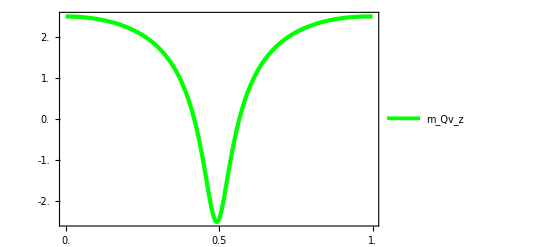

```mathematica
legends={StringForm["````",Subscript["m","Q"],Subscript["v","z"]]}
P11a = ListLinePlot[{pZTimeData}, PlotRange->All, 
Frame -> True, FrameTicks->  {    {{#,10^17 #}&/@FindDivisions[{-2. 10^-17,2. 10^-17},5] //N,Automatic},{{#,1000 #}&/@FindDivisions[{0.,.002},5] //N,Automatic}   } , LabelStyle->Directive[Black, FontSize -> 14], PlotLegends->Placed[{legends},{Right, Bottom}], PlotStyle-> {Directive[Thickness[0.0075], Green] } , InterpolationOrder->2 ]
```

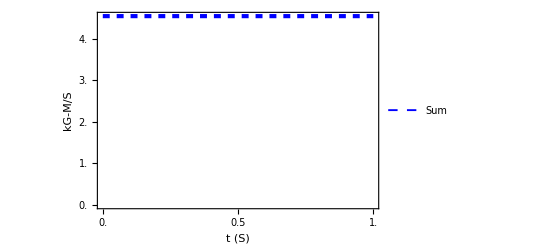

```mathematica
P12a = ListLinePlot[{Mass * VzTimeData + qAofXTimeData}, AxesLabel -> {"t (S)", "kG-M/S"}, PlotRange->All, Frame -> True, FrameTicks->  {    {{#,10^17 #}&/@FindDivisions[{0. 10^-17,5. 10^-17},5] //N,Automatic},{{#,1000 #}&/@FindDivisions[{0.,.002},5] //N,Automatic}   } , LabelStyle->Directive[Black, FontSize -> 14], PlotLegends->Placed[{"Sum"},{Right, Top}], PlotStyle-> {Directive[Dashed, Blue, Thickness[0.0075]]} ]
```

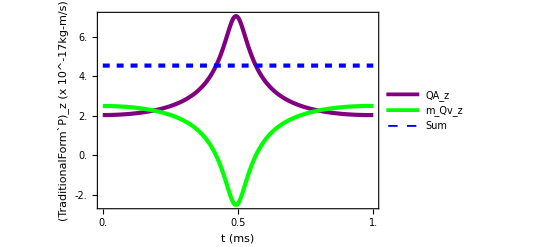

```mathematica
Show[P10a, P11a, P12a, PlotRange->All, AxesOrigin -> {0., -2. 10^-17}, ImageMargins->{{5,5},{10,5}} ]
```